Two atom basis lattice vibrations (phonon modes)

```mathematica
ClearAll[numFrequenciesPerQ, rcap, scap, vR, vS, rn, maxQ, alphaF, betaF, mA, mB, mM] ;

(* 4 angular frequencies for 2 atom basis *) 
numFrequenciesPerQ = 4 ;

rcap::usage = "rcap(theta)" ;
rcap = {Cos[#], Sin[#]} & ;
scap = {-Cos[#], Sin[#]} & ;

vR::usage = "vR(a, theta).  The North-east pointing primitive cell vector for the diamond lattice.  a is the length of this vector, and 2 theta is the angular separation of the pair of primitive cell vectors." ;
vR = #1 rcap[#2] & ;
vS = #1 scap[#2] &;

rn::usage = "rn({n1, n2}, a, theta).  This is the position of the origin of the {n1, n2} unit cell." ;
rn = #1[[1]] vR[#2, #3] + #1[[2]] vS[#2, #3]  &;

maxQ::usage = "maxQ(a, theta).  This is the maximum length for either of the reciprocal frame vectors for this diamond lattice.

Note that the reciprocal vectors are g = (Pi/a)(pm/Cos[theta], Sin[theta]), with norm: 2 Pi/(a Sin[2 theta]))" ;
maxQ = 2 Pi/(#1 Sin[2 #2]) & ;

alphaF::usage = "alphaF( a, theta, k3, pm k4, {qx, qy})" ;
alphaF = #3 Sin[vR[#1, #2] . #5/2]^2 + #4 Sin[vS[#1, #2]  . #5/2]^2 &;

betaF::usage = "betaF( a, theta, k1, pm k2, {qx, qy})" ;
betaF = #3 Cos[(vR[#1, #2] - vS[#1, #2] ) . #5/2] + #4 Cos[(vR[#1, #2] + vS[#1, #2] ) . #5/2]& ;

mA::usage = "mA(k1, k2, theta, alphaPlus, alphaMinus)" ;
mA = {{#1 + #4(1 + Cos[2 #3]), #5Sin[2 #3]} , {#5Sin[2 #3], #2 + #4(1 + Cos[2 #3])}} & ;

mB::usage = " mB(a, theta, qy, betaPlus, betaMinus) " ;
mB = E^(I #1 Sin[#2] #3){ 
{#4(1 + Cos[2 #2]), #5Sin[2 #2]} , {#5Sin[2 #2], #4(1 + Cos[2 #2])}} & ;

mM::usage = "This is the final matrix equation to solve for ω^2, and the corresponding eigenvectors {e1, e2}.

mM(#1,         #2,#3,#4,#5,#6,#7   ,#8       ,#9        ,#10     ,#11      ,#12)
mM(omegaSquare,k1,k2,m1,m2,a ,theta,alphaPlus,alphaMinus,betaPlus,betaMinus,qy)

See: https://sites.google.com/site/peeterjoot3/math2014/twoMassHarmonic.pdf to understand how this matrix equation was arrived at (and an explaination of the helper submatrix variables above).
" ;
mM=ArrayFlatten[{{#1 IdentityMatrix[2]-2 mA[#2,#3,#7,#8,#9]/#4,mB[#6,#7,-#12,#10,#11]/Sqrt[#4 #5]},{mB[#6,#7,#12,#10,#11]/Sqrt[#4 #5],#1 IdentityMatrix[2]-2 mA[#2,#3,#7,#8,#9]/#5}}]&;

(*
ClearAll[d] ;
d = Collect[ Det[ mM[## ] ], {#1, #4, #5}, Simplify] &;

(* display equation to solve for ω^2 *)
mM[ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]] // TraditionalForm // MatrixForm

(* A full expansion of the Determinant for above, Simplified term by term in powers of ω^2 *)
d[ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]] // TraditionalForm*) 
 
ClearAll[qTable] ;
qTable[p_] := Module[{k1, k2, k3, k4, m1, m2, a, theta,qIntervals,mE, alpha, beta, vv, qMax, f, e, t, len},
{k1, k2, k3, k4, m1, m2, a, theta, qIntervals} = p ;

qMax = maxQ[a, theta] ;

alpha[qq_, sign_] := alphaF[a, theta, k3, sign k4, qq] ;
beta[qq_, sign_] := betaF[a, theta, k1, sign k2, qq] ;

(*ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]*)
mE[qq_List] := -mM[0,k1, k2, m1, m2, a, theta, alpha[qq, 1], alpha[qq, -1], beta[qq, 1], beta[qq, -1], qq[[2]]] ;

(*f = mE[{-qMax/2, -qMax/2}] // N  ;
(*f*)
Eigensystem[f]*)

f = Flatten[ Table[ {qx, qy, mE[{qx, -qy}] // N},{qx, -qMax/2, qMax/2, qMax/qIntervals}, {qy, -qMax/2, qMax/2, qMax/qIntervals}], 1] ;
e = Eigensystem[ #[[3]] ] &/@ f ;
(*e*)
len = Length[e] ;

t= Table[
Sort[{Sqrt[#[[1]]], Take[#[[2]], 2], Drop[#[[2]], 2]} &/@ (e[[i]] // Transpose), #1[[1]] < #2[[1]] &], {i, len}] ;
(*t*)

Table[{Take[f[[i]], 2], t[[i]]}, {i, len}]
] ;

ClearAll[resultsForOneQpoint] ;
resultsForOneQpoint::usage = "Consume intermediate results of qTable[] and rescale the e1,e2 eigenvector components by the masses." ;
resultsForOneQpoint[{m1_, m2_}, j_, i_, results_]:= Module[{q, omega, e1, e2},

q = results[[j]][[1]] ;
{omega, e1, e2} = results[[j]][[2]][[i]] ;

{
q, 
omega,
e1/Sqrt[ m1 ],
e2/Sqrt[ m2]

}
] ;

ClearAll[ functionsCompute ] ;
functionsCompute::usage = "functionsCompute({k1, k2, k3, k4, m1, m2, a, theta, qi})" ;
functionsCompute[p_]:= Module[{r, f},

r = qTable[p]  ;

f = Flatten[Table[
resultsForOneQpoint[Take[p, {5,6}] (* {m1, m2} *) , j, i, r]
, {j, Length[r]}
,{i, numFrequenciesPerQ} 
],1] ;

f
] ;

(* These spring functions are from: http://mathematica.stackexchange.com/a/37228/10 ... they aren't very pretty, but do the job. *)

ClearAll[ unitSpringPoints, coordinateTrasformMatrix, coordinateTransform, spring ] ;

unitSpringPoints::usage = "This is a spring connecting {0,0} and {1,0} with two small horizontal segment at the end points (that is the reason for generating two separate lists).To show the spring just wrap a Line around the generated points,like this

Show[Graphics[Line[unitSpringPoints[5,0.25]]]]" ;
unitSpringPoints[n_,h_]:=Block[{dl,xlist,ylist},dl=1/(2 n+1);
xlist=Flatten[{0,1.5 dl,dl Table[k,{k,2,2 n-1}],1-1.5 dl,1}];
ylist=Flatten[{0,0,h/2 Table[(-1)^(k+1),{k,2,2 n-1}],0,0}];
Transpose[{xlist,ylist}]]

coordinateTrasformMatrix::usage = "Next I defined a function to transform coordinates in order to produce a spring between two given points {x0,y0} and {x1,y1}.Since this is very old code,I defined my own transformation matrix as in" ;
coordinateTrasformMatrix[{x0_,y0_},{x1_,y1_}]:=Block[{theta},theta=ArcTan[(x1-x0),(y1-y0)];
{{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}}] ;


coordinateTransform::usage = "And then I used it to transform the coordinates of the points of the the unit spring in those of the points of the spring between the given points" ;
coordinateTransform[coords_List,{{x0_,y0_},{x1_,y1_}}]:=Block[{scale,mat},scale=Sqrt[(x1-x0)^2+(y1-y0)^2];
mat=coordinateTrasformMatrix[{x0,y0},{x1,y1}];
({x0,y0}+mat.({scale,1}*#))&/@coords] ;

spring::usage = "Then,a spring with n coils and aspect ratio h between points {x0,y0} and {x1,y1} would be given by
For example:

Show[Graphics[spring[{{2,2},{3,3}},8,0.25]],AspectRatio→Automatic]
Show[Graphics[spring[{{0,0},{0,1}},8,0.25]],AspectRatio→Automatic]" ;
spring[{{x0_,y0_},{x1_,y1_}},n_:8,h_:.25]:=Line[coordinateTransform[unitSpringPoints[n,h],{{x0,y0},{x1,y1}}]] ;
```

```mathematica
Manipulate[
DynamicModule[{  qi, params, functions  },

qi = 2 ;

params ={k1, k2, k3, k4, m1, m2, a, theta, qi} ;

(*functions = {1, 2,3} ;*)
(*functions = qTable[params] ;*)
(*functions = params ;*)
functions = functionsCompute[ params ] ;
(*functions = Module[{r, f},

r = qTable[params]  ;

f = Flatten[Table[
resultsForOneQpoint[ {m1, m2} , j, i, r]
, {j, Length[r]}
,{i, numFrequenciesPerQ} 
],1] ;

f
] ;*)

If[ False,

{Take[functions, {1,2}], qManip, n, tau}, (* debug *)

DynamicModule[{q,omega,e1, e2, exp, rN,g0,g1, g2, pointsRange, points1, points2, lines },

q = 2Pi Round[qManip qi/2]/(qi a Sin[2 theta] ) ;
{omega, e1, e2} = Take[ Select[ functions, #[[1]] == q & ][[n]], -3] ;

(* f(vecR, t, eN) *)
exp := Re[#3 Exp[ I(#1 . q - omega #2) ] ] &;

rN = rn[ #, a, theta ] & ;
g0 = rN[#] + {0, a Sin[ theta ]/2}  & ;

g1 = g0[#1]  + exp[ rN[#1],#2, e1 ] & ;
g2= g0[#1] + {0, a Sin[theta]} + exp[ rN[#1],#2, e2 ] & ;

(* functions of time. *)
pointsRange = 2 ;
points1 = Flatten[ Table[ g1[{i, j}, #], {i, -pointsRange-1, pointsRange}, {j, -pointsRange-1, pointsRange}], 1 ] & ;
points2 = Flatten[ Table[ g2[{i, j}, #], {i, -pointsRange-1, pointsRange}, {j, -pointsRange-1, pointsRange}], 1 ] & ;

lines = Flatten[ {
Table[ { 
rN[{i, -3}],
rN[{i, 3}]
} ,{i, -3, 3}],
Table[ { 
rN[{-3, i}],
rN[{3, i}]
} ,{i, -3, 3}]}, 1] ;

Column[{
Row[{OverVector["q"]," = ", q // MatrixForm}],
Row[{"ω = ", omega}],
Module[{mList1, mList2, prange, bothLists},
mList1 = {g1[{-1, 0}, 0], g1[{0, 0}, 0], g1[{0, -1}, 0], g1[{1, 0}, 0], g1[{0, 1}, 0]} ;
mList2 = {g2[{-1, 0}, 0], g2[{0, 0}, 0], g2[{0, -1}, 0], g2[{-1, -1}, 0]} ;
bothLists = Flatten[ {mList1, mList2}, 1] // Transpose ;
prange = { Min[ bothLists[[#]] ], Max[ bothLists[[#]] ] } * 1.1 &;

ListLinePlot[lines
, PlotRange -> (prange[#] &/@ Range[2])
, Epilog -> {
PointSize[Sqrt[m1]/200],Red, Point[ mList1]
,Blue, PointSize[Sqrt[m2]/200],Point[mList2]
,Text[ "m_1", g1[{0, 0}, 0] + {0.05, 0} ]
,Text[ "m_2", g2[{0, 0}, 0] + {0.05, 0} ]

,spring[{g2[{-1, 0}, 0], g1[{0, 0}, 0]}, 10, 0.1]
,spring[{g1[{0, 1}, 0], g1[{0, 0}, 0]}, 10, 0.05]
,spring[{g1[{-1, 0}, 0], g1[{0, 0}, 0]}, 10, 0.05]
,spring[{g1[{0, 0}, 0], g2[{0, 0}, 0]}, 10, 0.05]

,spring[{g1[{1, 0}, 0], g1[{0, 0}, 0]}, 10, 0.05]
,spring[{g1[{0, -1}, 0], g1[{0, 0}, 0]}, 10, 0.05]
,spring[{g2[{0, -1}, 0], g1[{0, 0}, 0]}, 10, 0.1]
,spring[{g1[{0, 0}, 0], g2[{-1, -1}, 0]}, 10, 0.05]

(* labels at the midpoints *)
,Text["k_3",(g1[{-1, 0}, 0]+ g1[{0, 0}, 0])/2 + {0.05, -0.05}]
,Text["k_1",(g2[{-1, 0}, 0]+ g1[{0, 0}, 0])/2 + {0,0.05}]
,Text["k_2", (g2[{-1, -1}, 0]+ g1[{0, 0}, 0])/2 + {0.05, 0}]
,Text["k_4",(g1[{0, 1}, 0]+ g1[{0, 0}, 0])/2 + {0.05, 0.05}]
}
]
],
ListLinePlot[lines
, PlotRange -> {{-2, 2}, {-2, 2}}
, Epilog -> {PointSize[Sqrt[m1]/200],Red, Point[points1[2 Pi tau/omega]], Blue, PointSize[Sqrt[m2]/200],Point[points2[2 Pi tau/omega]]}
]
}]
]
] (* If *)
]
,{{k1, 0.5, "k_1"}, 0.25, 0.9,Appearance->"Labeled"}
,{{k2, 0.5, "k_2"}, 0.25, 0.9,Appearance->"Labeled"}
,{{k3, 0.25, "k_3"}, 0.25, 0.9,Appearance->"Labeled"}
,{{k4, 0.25, "k_4"}, 0.25, 0.9,Appearance->"Labeled"}
,{{m1, 10, "m_1"}, 5, 30,Appearance->"Labeled"}
,{{m2, 20, "m_2"}, 5, 30,Appearance->"Labeled"}
,{{a, 1, "a"}, 0.5, 2,Appearance->"Labeled"}
,{{theta, Pi/3, "θ"},Pi/3, 4 Pi/8,Appearance->"Labeled"}
(*,{{qi, 4, "q mesh size"}, 4, 4}*)
,{{n, 1, "ω_n: n = "}, 1, numFrequenciesPerQ, 1, Appearance->"Labeled"}
, {{qManip,{0,0},OverVector["q"]},{-1, -1}, {1, 1} }
, {{tau, 0, "t/T"}, 0, 1}
, SaveDefinitions->True
(*, TrackedSymbols:>{k1, k2, k3, k4, m1, m2, a, theta}*)
(*,Initialization:> {
qi = 4 ;
pointsRange = 2 ;
}*)
]
```

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbour atoms.  In this demonstration, a lattice containing pairs of atoms, each with separate masses is modelled, with nearest neighbour harmonic coupling for each mass.  Normal mode solutions to these equations of motion are plotted, with controls provided to alter the coupling "spring constants" and other free parameters.

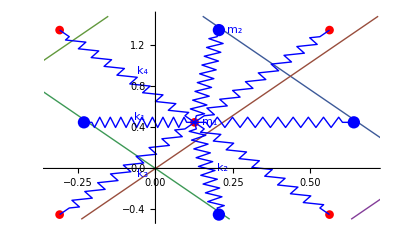

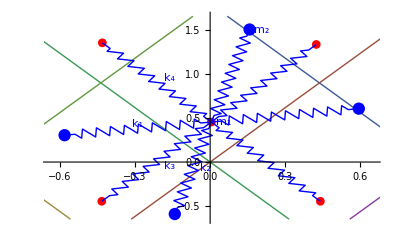
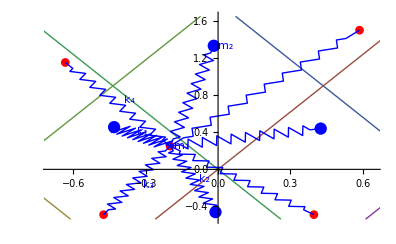
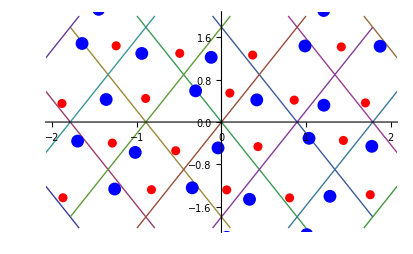
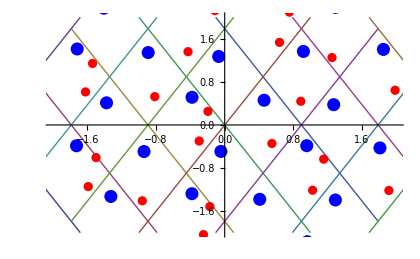

Trial solutions of the form: (u⃗)_(n,i)(r_n', t)= (OverVector[ϵ_i](q⃗))/(√m_i)e^(I (OverVector[r_(n⃗)]. q⃗ - ω t)) are used to find solutions for the system.

Here (u⃗)_(n,i)is a vector displacement for the mass in unit cell n, for mass i ; (r⃗)_(n⃗ = (n_1, n_2)) = n_1 s⃗ + n_2 t⃗ is the position of the n⃗'th unit cell, and s⃗,t⃗ are the unit cell vectors ; q⃗ is a vector in reciprocal space.  The vectors OverVector[ϵ_i](q) together form an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For this two atom basis, there are four such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.  A control is available to pick between these characteristic angular frequencies.

Free parameters availble as controls in this demonstration include the spring constants k_i, the masses m_i, the primative unit cell lattice vectors (±a cos(θ), sin(θ)).  With each such selection, an additional selector is available to choose the reciprocal vector q⃗.

General theory describing oscillations around the lattice equilbrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

two atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Contributed by: Peeter Joot